```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

### Plot a Lorentzian profiles of the surface, plot1

```mathematica
A=800000;
a=80;
b=0.0007;
λ0=512;
js={60,100,120,140,180};
surf=Function[{x,y},A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((y-512)^2+a^2)];
height=Function[x,A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((λ0-512)^2+a^2)](*Half height at position j, same as surf but without (u-λ0)^2*);
```

```mathematica
plot1=ParametricPlot3D[
Table[{j,u,surf[j,u]},{j,js}],{u,0,1024},
ImageSize->Large
]
```

-Graphics3D-

#### Labels and arrows of FWHM

```mathematica
Δλ=Text[Style["Δλ",Bold,Black,20],{Last[js],λ0,height[Last[js]]/2-15}];
xlabel=Text[Style["x-coordinate\n[px]",Bold,Black,20],{256,0,0}];
ylabel=Text[Style["λ [nm]",Bold,Black,20],{0,1024,0}];
zlabel=Text[Style["Intensity",Bold,Black,20],{0,0,130}];
```

```mathematica
ω=0.015;(*arrow size*)
arrows=Table[
{Arrowheads[{-ω,ω}],
Arrow[{{j,λ0-a,height[j]/2},{j,λ0+a,height[j]/2}}]},
{j,js}
];
```

### Plot the Lorentzians with the arrows and labels, plot2:

```mathematica
faceGridPositions={{{0,0,-1},{Range[0,256,30],Range[0,1024,30]}}};
plot2=Show[{
Graphics3D[xlabel],
Graphics3D[ylabel],
Graphics3D[zlabel],
Graphics3D[arrows],
Graphics3D[Δλ],
plot1
},
Axes->True,
AxesStyle->Thick,
Boxed->False
,Ticks->{{512,256},None,None}
,AxesOrigin->{0,0,0}
,PlotRange->{{0,256},{0,1024},{0,130}}
,ViewPoint->{10,40,10}
,ViewVertical->{0,0,9}
,ImageSize->Full
,FaceGrids->faceGridPositions
,FaceGridsStyle->Directive[Gray,Dashed]]
```

-Graphics3D-

For a lorentzian of the form used here, f(x)=1/((x-X)^2+a^2):
The half maximum is at x→X-a, x→X+a, i.e., fwhm =2a.
f(X-a)=f(X+a)=1/(2 a^2).

### Plot the mesh of the surface, plot3:

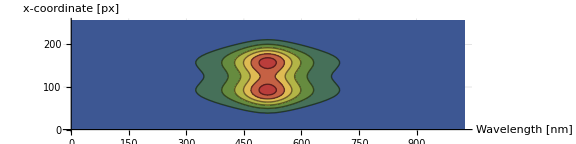

```mathematica
r=120;
b=0.0007;
plot3=ContourPlot[surf[y,x],{x,0,1024},{y,0,256},
PlotRange->Full,
ColorFunction->"DarkRainbow",
AspectRatio->1/4,
Axes->True,
AxesLabel->{"Wavelength [nm]","x-coordinate\n[px]"},
GridLines->Automatic,
Frame->False,
ImageSize->Large]
```

### Plot the 3 plots in a grid

```mathematica
Import["blue arrows-down.pdf"]⟦1⟧
```

-Graphics-

```mathematica
Import["blue arrows-right.pdf"]⟦1⟧
```

-Graphics-

```mathematica
Grid[{{plot3, □, □}, {-Graphics-, □, □}, {plot2, -Graphics-, plot1}}]
```

```mathematica
Export["C:\\Users\\HILL\\Desktop\\grid.pdf",Grid[{{plot3, □, □}, {-Graphics-, □, □}, {plot2, -Graphics-, plot1}}]]
```